External and internal quantum state transfer between two ions via two collective field modes in a array of coupled cavities

### Case (A) - System of differential equations of first order

```mathematica
Clear[eq1,eq2,eq3,eq4,eq5,ceg1000,cgg2001,cgg0010,cge0100,cgg0201,gef,η,g,ωa,ν]
gef=η g /√2;
eq1=I*D[ceg1000[t],{t,1}]==gef cgg0010[t] + √2 gef cgg2001[t]*Exp[-2 I*Δ*t];
eq2=I*D[cgg2001[t],{t,1}]==√2 gef ceg1000[t]*Exp[2I*Δ*t];
eq3=I*D[cgg0010[t],{t,1}]== gef ceg1000[t] + gef cge0100[t];
eq4=I*D[cge0100[t],{t,1}]==gef cgg0010[t] -√2 gef cgg0201[t]*Exp[-2I*Δ*t];
eq5=I*D[cgg0201[t],{t,1}]== -√2 gef cge0100[t]*Exp[2I*Δ*t];
```

### Case (A) - Analytical Solution

```mathematica
Clear[linha1,linha2,linha3,linha4,linha5]
linha1=LaplaceTransform[eq1,t,s-I Δ]
linha2=LaplaceTransform[eq2,t,s+I Δ]
linha3=LaplaceTransform[eq3,t,s-I Δ]
linha4=LaplaceTransform[eq4,t,s-I Δ]
linha5=LaplaceTransform[eq5,t,s+I Δ]
```

ⅈ (-ceg1000[0]+(s-ⅈ Δ) LaplaceTransform[ceg1000[t],t,s-ⅈ Δ])==(g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])/(√2)+g η LaplaceTransform[cgg2001[t],t,s+ⅈ Δ]

ⅈ (-cgg2001[0]+(s+ⅈ Δ) LaplaceTransform[cgg2001[t],t,s+ⅈ Δ])==g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]

ⅈ (-cgg0010[0]+(s-ⅈ Δ) LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])==(g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ])/(√2)+(g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ])/(√2)

ⅈ (-cge0100[0]+(s-ⅈ Δ) LaplaceTransform[cge0100[t],t,s-ⅈ Δ])==(g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])/(√2)-g η LaplaceTransform[cgg0201[t],t,s+ⅈ Δ]

ⅈ (-cgg0201[0]+(s+ⅈ Δ) LaplaceTransform[cgg0201[t],t,s+ⅈ Δ])==-g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ]

```mathematica
Clear[linhas]
linhas={};
linha11=ceg1000[0]/.Solve[linha1,ceg1000[0]][[1]]
linha22=cgg2001[0]/.Solve[linha2,cgg2001[0]][[1]]
linha33=cgg0010[0]/.Solve[linha3,cgg0010[0]][[1]]
linha44=cge0100[0]/.Solve[linha4,cge0100[0]][[1]]
linha55=cgg0201[0]/.Solve[linha5,cgg0201[0]][[1]]
AppendTo[linhas,linha11]; AppendTo[linhas,linha22]; AppendTo[linhas,linha33]; AppendTo[linhas,linha44]; AppendTo[linhas,linha55];
```

s LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+1/2 ⅈ (-2 Δ LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+√2 g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ]+2 g η LaplaceTransform[cgg2001[t],t,s+ⅈ Δ])

s LaplaceTransform[cgg2001[t],t,s+ⅈ Δ]+ⅈ (g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+Δ LaplaceTransform[cgg2001[t],t,s+ⅈ Δ])

s LaplaceTransform[cgg0010[t],t,s-ⅈ Δ]+1/2 ⅈ (√2 g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+√2 g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ]-2 Δ LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])

s LaplaceTransform[cge0100[t],t,s-ⅈ Δ]+1/2 ⅈ (-2 Δ LaplaceTransform[cge0100[t],t,s-ⅈ Δ]+√2 g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ]-2 g η LaplaceTransform[cgg0201[t],t,s+ⅈ Δ])

s LaplaceTransform[cgg0201[t],t,s+ⅈ Δ]+ⅈ (-g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ]+Δ LaplaceTransform[cgg0201[t],t,s+ⅈ Δ])

```mathematica
u={LaplaceTransform[ceg1000[t],t,s-ⅈ Δ],LaplaceTransform[cgg2001[t],t,s+ⅈ Δ],LaplaceTransform[cgg0010[t],t,s-ⅈ Δ],LaplaceTransform[cge0100[t],t,s-ⅈ Δ],LaplaceTransform[cgg0201[t],t,s+ⅈ Δ]};
```

```mathematica
M=Table[0,{i,5},{j,5}];
For[i=1,i<6,i++,
For[j=1,j<6,j++,
M[[i,j]]=Coefficient[linhas[[i]],u[[j]]];
]
]
M //MatrixForm
```

(s-ⅈ Δ | ⅈ g η | (ⅈ g η)/(√2) | 0 | 0
ⅈ g η | s+ⅈ Δ | 0 | 0 | 0
(ⅈ g η)/(√2) | 0 | s-ⅈ Δ | (ⅈ g η)/(√2) | 0
0 | 0 | (ⅈ g η)/(√2) | s-ⅈ Δ | -ⅈ g η
0 | 0 | 0 | -ⅈ g η | s+ⅈ Δ)

```mathematica
Clear[S,Feg1000,Fgg2001,Fgg0010,Fge0100,Fgg0201]
S={Feg1000[s-ⅈ Δ],Fgg2001[s+ⅈ Δ],Fgg0010[s-ⅈ Δ],Fge0100[s-ⅈ Δ],Fgg0201[s+ⅈ Δ]};
```

```mathematica
Clear[CC,ceg1000ini,cgg2001ini,cgg0010ini,cge0100ini,cgg0201ini,Δ]
CC={ceg1000ini,cgg2001ini,cgg0010ini,cge0100ini,cgg0201ini};
ceg1000ini=-Sin[θ];
cgg2001ini=0;
cgg0010ini=0;
cge0100ini=0;
cgg0201ini=0;
CF={Cos[θ],0,0,0,Sin[θ],0};
```

```mathematica
Feg1000[s-ⅈ Δ]=(Inverse[M].CC)[[1]];
Fgg2001[s+ⅈ Δ]=(Inverse[M].CC)[[2]];
Fgg0010[s-ⅈ Δ]=(Inverse[M].CC)[[3]];
Fge0100[s-ⅈ Δ]=(Inverse[M].CC)[[4]];
Fgg0201[s+ⅈ Δ]=(Inverse[M].CC)[[5]];
```

```mathematica
Ceg1000[t_,θ_,Δ_]=InverseLaplaceTransform[Feg1000[s-ⅈ Δ],s,t];
Cgg2001[t_,θ_,Δ_]=InverseLaplaceTransform[Fgg2001[s+ⅈ Δ],s,t];
Cgg0010[t_,θ_,Δ_]=InverseLaplaceTransform[Fgg0010[s-ⅈ Δ],s,t];
Cge0100[t_,θ_,Δ_]=InverseLaplaceTransform[Fge0100[s-ⅈ Δ],s,t];
Cgg0201[t_,θ_,Δ_]=InverseLaplaceTransform[Fgg0201[s+ⅈ Δ],s,t];
Cgg0000[t_,θ_,Δ_]=Cos[θ];
```

```mathematica
Clear[AA,BB,CC,ωa,η,g,ν]
AA[t_]=ⅈ  ωa t;
BB[t_]=-ⅈ  ν t;
CC[t_]=-ⅈ (2 Δ+ ν ) t;
```

```mathematica
Clear[Ψs,CSgg0000,CSeg1000,CSgg2001,CSgg0010,CSge0100,CSgg0201]
Ψs={CSgg0000[t,θ,Δ,η,g,ωa,ν],CSeg1000[t],CSgg2001[t],CSgg0010[t],CSge0100[t],CSgg0201[t]};
CSgg0000[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[AA[t]] Cgg0000[t,θ,Δ];
CSeg1000[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[BB[t]] Ceg1000[t,θ,Δ];
CSgg2001[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[CC[t]] Cgg2001[t,θ,Δ];
CSgg0010[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[BB[t]] Cgg0010[t,θ,Δ];
CSge0100[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[BB[t]] Cge0100[t,θ,Δ];
CSgg0201[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[CC[t]] Cgg0201[t,θ,Δ];
```

```mathematica
Ψs={CSgg0000[t,θ,Δ,η,g,ωa,ν],CSeg1000[t,θ,Δ,η,g,ωa,ν],CSgg2001[t,θ,Δ,η,g,ωa,ν],CSgg0010[t,θ,Δ,η,g,ωa,ν],CSge0100[t,θ,Δ,η,g,ωa,ν],CSgg0201[t,θ,Δ,η,g,ωa,ν]};
ρA=Table[0,{i,6},{j,6}];
For[i=1,i≤6,i++,
For[j=1,j≤6,j++,
ρA[[i,j]]=Ψs[[i]]*Conjugate[Ψs[[j]]];
]
]
```

### Case (A) - Functions and Parameters

```mathematica
Clear[ωa0,η0,g0,ν0]
η0=0.1;
g0=20;
ωa0=90;
ν0=30;
λ0=27.5;
Δ0=ν0-λ0
θ0=π/4;

(* Norm of the vector state of the system *)
norm[t_]=Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on ion 1 *)
f1[t_]=Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on ion 2 *)
f2[t_]=Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on resonant collective mode *)
f3[t_]=Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on off resonant collective mode *)
f4[t_]=Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Population inversion of degrees on freedom of ion 1*)
inv1[t_]=Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Population inversion of degrees on freedom of ion 2*)
inv2[t_]=Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Population inversion of degrees on freedom of resonant collective mode *)
inv3[t_]=Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Population inversion of degrees on freedom of off resonant collective mode *)
inv4[t_]=Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Fidelity of the QST from ion 1 to ion 2 *)
fid[t_]=Abs[Cos[θ0]CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]+ Sin[θ0]CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
fid2[g_]=Abs[Cos[θ0]CSgg0000[π,θ0,Δ0,1,g,ωa0,ν0]+ Sin[θ0]CSge0100[π,θ0,Δ0,1,g,ωa0,ν0]]^2;
(* Fidelity of the QST from ion 1 to ion 2 also in function of Δ*)
fid3D[t_,Δ_]=Simplify[N[Abs[Cos[θ0]CSgg0000[t,θ0,Δ,η0,g0,ωa0,ν0]+ Sin[θ0]CSge0100[t,θ0,Δ,η0,g0,ωa0,ν0]]^2]];
fid3D2[t_,θ_]=Simplify[N[Abs[Cos[θ]CSgg0000[t,θ,Δ0,η0,g0,ωa0,ν0]+ Sin[θ]CSge0100[t,θ,Δ0,η0,g0,ωa0,ν0]]^2]];
```

2.5

### Case (A) - Graphics and Results

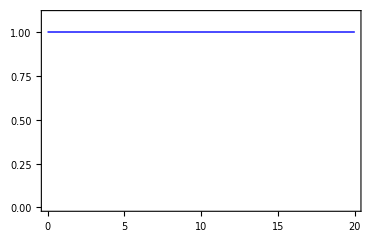

```mathematica
Plot[norm[t],{t,0,20},PlotRange->{0,1.1},Frame->True,PlotStyle->{Blue,Thick}]
```

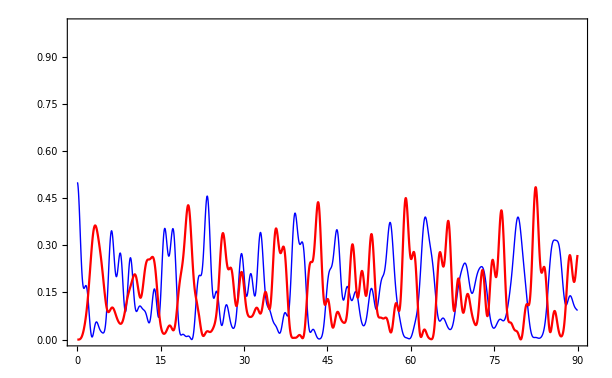

```mathematica
Plot[{f1[t/(η0 g0)],f2[t/(η0 g0)]},{t,0,90},PlotRange->{0,1},Frame->True,PlotStyle->{{Blue,Thick},Red}]
```

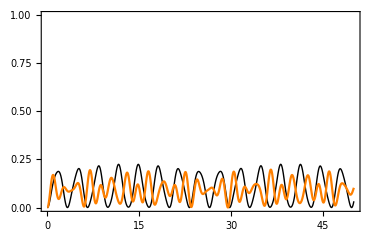

```mathematica
Plot[{f3[t/(η0 g0)],f4[t/(η0 g0)]},{t,0,50},PlotRange->{0,1},Frame->True,PlotStyle->{{Thick,Black},Orange}]
```

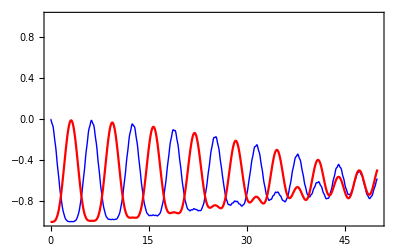

```mathematica
Plot[{inv1[t/(η0 g0)],inv2[t/(η0 g0)]},{t,0,50},PlotRange->{-1,1},Frame->True,PlotStyle->{{Blue,Thick},Red}]
```

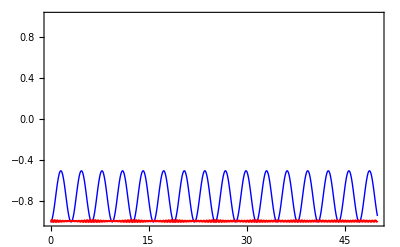

```mathematica
Plot[{inv3[t/(η0 g0)],inv4[t/(η0 g0)]},{t,0,50},PlotRange->{-1,1},Frame->True,PlotStyle->{{Blue,Thick},Red}]
```

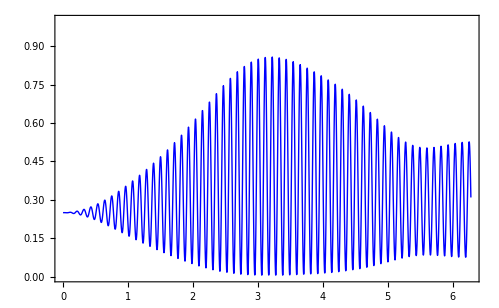

```mathematica
Plot[fid[t/(η0 g0)],{t,0,2π},PlotRange->{0,1},Frame->True,PlotStyle->{Blue,Thick},PlotPoints->40]
```

```mathematica
dt=0.00001;
tn=Range[2.,4,dt];
fn=Chop[fid[tn/(η0 g0)]];
Max[fn] (* Max fidelity *)
```

0.994021

```mathematica
k=Ordering[fn,-1][[1]];
tk = k*dt + 2 (* QST time *)
```

3.11464

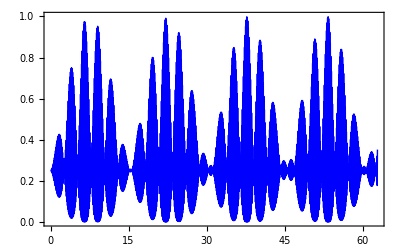

```mathematica
Plot[fid[t/(η0 g0)],{t,0,20π},PlotRange->{0,1},Frame->True,PlotStyle->{Blue,Thick},PlotPoints->500]
```

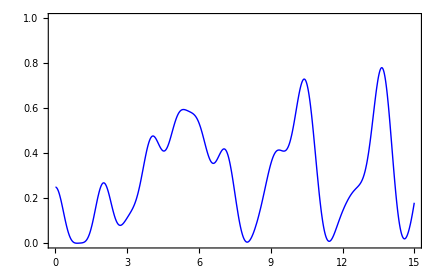

```mathematica
Plot[fid2[g],{g,0,Δ0},PlotRange->{0,1},Frame->True,PlotStyle->{Blue,Thick}]
```

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,3.5},{Δ,0.001,10},Mesh->Automatic,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

$Aborted

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,2π},{Δ,0.001,20},Mesh->Automatic,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->65,AspectRatio->1/2,FrameLabel->{"Time (Units of ηg)","Δ (Units of ηg)"},LabelStyle->Directive[14,Black]]
```

-Graphics-

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,2π},{Δ,0.001,20},Mesh->3,MeshFunctions->{#3 &},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70,AspectRatio->1/2,FrameLabel->{"Time (Units of ηg)","Δ (Units of ηg)"},LabelStyle->Directive[14,Black]]
```

-Graphics-

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,2π},{Δ,0.001,20},Mesh->None,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70,AspectRatio->1/2,FrameLabel->{"Time (Units of ηg)","Δ (Units of ηg)"},LabelStyle->Directive[15,Black]]
```

-Graphics-

```mathematica
ContourPlot[fid3D2[t/(η0 g0),θ],{t,0,3.5},{θ,0,π/2},Mesh->None,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

-Graphics-

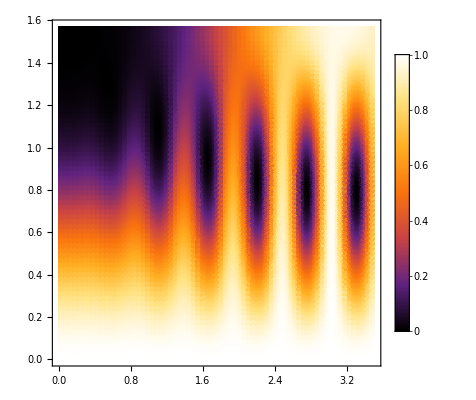

```mathematica
DensityPlot[fid3D2[t/(η0 g0),θ],{t,0,3.5},{θ,0,π/2},Mesh->None,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

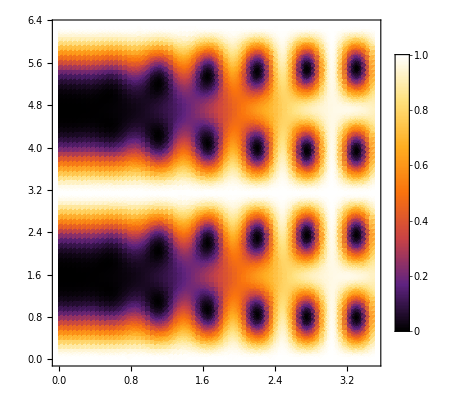

```mathematica
DensityPlot[fid3D2[t/(η0 g0),θ],{t,0,3.5},{θ,0,2π},Mesh->None,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

### Case (B) - System of differential equations of first order

```mathematica
Clear[eq1,eq2,eq3,eq4,eq5,ceg1000,cgg2001,cgg0010,cge0100,cgg0201,gef,η,g,ωa,ν]
gef=η g /√2;
eq1=I*D[ceg1000[t],{t,1}]==gef cgg0010[t] + √2 gef cgg2001[t]*Exp[-2 I*Δ*t];
eq2=I*D[cgg2001[t],{t,1}]==√2 gef ceg1000[t]*Exp[2I*Δ*t];
eq3=I*D[cgg0010[t],{t,1}]== gef ceg1000[t] + gef cge0100[t];
eq4=I*D[cge0100[t],{t,1}]==gef cgg0010[t] -√2 gef cgg0201[t]*Exp[-2I*Δ*t];
eq5=I*D[cgg0201[t],{t,1}]== -√2 gef cge0100[t]*Exp[2I*Δ*t];
```

### Case (B) - Analytical Solution

```mathematica
Clear[linha1,linha2,linha3,linha4,linha5]
linha1=LaplaceTransform[eq1,t,s-I Δ]
linha2=LaplaceTransform[eq2,t,s+I Δ]
linha3=LaplaceTransform[eq3,t,s-I Δ]
linha4=LaplaceTransform[eq4,t,s-I Δ]
linha5=LaplaceTransform[eq5,t,s+I Δ]
```

ⅈ (-ceg1000[0]+(s-ⅈ Δ) LaplaceTransform[ceg1000[t],t,s-ⅈ Δ])==(g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])/(√2)+g η LaplaceTransform[cgg2001[t],t,s+ⅈ Δ]

ⅈ (-cgg2001[0]+(s+ⅈ Δ) LaplaceTransform[cgg2001[t],t,s+ⅈ Δ])==g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]

ⅈ (-cgg0010[0]+(s-ⅈ Δ) LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])==(g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ])/(√2)+(g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ])/(√2)

ⅈ (-cge0100[0]+(s-ⅈ Δ) LaplaceTransform[cge0100[t],t,s-ⅈ Δ])==(g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])/(√2)-g η LaplaceTransform[cgg0201[t],t,s+ⅈ Δ]

ⅈ (-cgg0201[0]+(s+ⅈ Δ) LaplaceTransform[cgg0201[t],t,s+ⅈ Δ])==-g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ]

```mathematica
Clear[linhas]
linhas={};
linha11=ceg1000[0]/.Solve[linha1,ceg1000[0]][[1]]
linha22=cgg2001[0]/.Solve[linha2,cgg2001[0]][[1]]
linha33=cgg0010[0]/.Solve[linha3,cgg0010[0]][[1]]
linha44=cge0100[0]/.Solve[linha4,cge0100[0]][[1]]
linha55=cgg0201[0]/.Solve[linha5,cgg0201[0]][[1]]
AppendTo[linhas,linha11]; AppendTo[linhas,linha22]; AppendTo[linhas,linha33]; AppendTo[linhas,linha44]; AppendTo[linhas,linha55];
```

s LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+1/2 ⅈ (-2 Δ LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+√2 g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ]+2 g η LaplaceTransform[cgg2001[t],t,s+ⅈ Δ])

s LaplaceTransform[cgg2001[t],t,s+ⅈ Δ]+ⅈ (g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+Δ LaplaceTransform[cgg2001[t],t,s+ⅈ Δ])

s LaplaceTransform[cgg0010[t],t,s-ⅈ Δ]+1/2 ⅈ (√2 g η LaplaceTransform[ceg1000[t],t,s-ⅈ Δ]+√2 g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ]-2 Δ LaplaceTransform[cgg0010[t],t,s-ⅈ Δ])

s LaplaceTransform[cge0100[t],t,s-ⅈ Δ]+1/2 ⅈ (-2 Δ LaplaceTransform[cge0100[t],t,s-ⅈ Δ]+√2 g η LaplaceTransform[cgg0010[t],t,s-ⅈ Δ]-2 g η LaplaceTransform[cgg0201[t],t,s+ⅈ Δ])

s LaplaceTransform[cgg0201[t],t,s+ⅈ Δ]+ⅈ (-g η LaplaceTransform[cge0100[t],t,s-ⅈ Δ]+Δ LaplaceTransform[cgg0201[t],t,s+ⅈ Δ])

```mathematica
u={LaplaceTransform[ceg1000[t],t,s-ⅈ Δ],LaplaceTransform[cgg2001[t],t,s+ⅈ Δ],LaplaceTransform[cgg0010[t],t,s-ⅈ Δ],LaplaceTransform[cge0100[t],t,s-ⅈ Δ],LaplaceTransform[cgg0201[t],t,s+ⅈ Δ]};
```

```mathematica
M=Table[0,{i,5},{j,5}];
For[i=1,i<6,i++,
For[j=1,j<6,j++,
M[[i,j]]=Coefficient[linhas[[i]],u[[j]]];
]
]
M //MatrixForm
```

(s-ⅈ Δ | ⅈ g η | (ⅈ g η)/(√2) | 0 | 0
ⅈ g η | s+ⅈ Δ | 0 | 0 | 0
(ⅈ g η)/(√2) | 0 | s-ⅈ Δ | (ⅈ g η)/(√2) | 0
0 | 0 | (ⅈ g η)/(√2) | s-ⅈ Δ | -ⅈ g η
0 | 0 | 0 | -ⅈ g η | s+ⅈ Δ)

```mathematica
Clear[S,Feg1000,Fgg2001,Fgg0010,Fge0100,Fgg0201]
S={Feg1000[s-ⅈ Δ],Fgg2001[s+ⅈ Δ],Fgg0010[s-ⅈ Δ],Fge0100[s-ⅈ Δ],Fgg0201[s+ⅈ Δ]};
```

```mathematica
Clear[CC,ceg1000ini,cgg2001ini,cgg0010ini,cge0100ini,cgg0201ini,Δ]
CC={ceg1000ini,cgg2001ini,cgg0010ini,cge0100ini,cgg0201ini};
ceg1000ini=Sin[θ];
cgg2001ini=0;
cgg0010ini=0;
cge0100ini=0;
cgg0201ini=0;
CF={Cos[θ],0,0,0,Sin[θ],0};
```

```mathematica
Feg1000[s-ⅈ Δ]=(Inverse[M].CC)[[1]];
Fgg2001[s+ⅈ Δ]=(Inverse[M].CC)[[2]];
Fgg0010[s-ⅈ Δ]=(Inverse[M].CC)[[3]];
Fge0100[s-ⅈ Δ]=(Inverse[M].CC)[[4]];
Fgg0201[s+ⅈ Δ]=(Inverse[M].CC)[[5]];
```

```mathematica
Ceg1000[t_,θ_,Δ_]=InverseLaplaceTransform[Feg1000[s-ⅈ Δ],s,t];
Cgg2001[t_,θ_,Δ_]=InverseLaplaceTransform[Fgg2001[s+ⅈ Δ],s,t];
Cgg0010[t_,θ_,Δ_]=InverseLaplaceTransform[Fgg0010[s-ⅈ Δ],s,t];
Cge0100[t_,θ_,Δ_]=InverseLaplaceTransform[Fge0100[s-ⅈ Δ],s,t];
Cgg0201[t_,θ_,Δ_]=InverseLaplaceTransform[Fgg0201[s+ⅈ Δ],s,t];
Cgg0000[t_,θ_,Δ_]=Cos[θ];
```

```mathematica
Clear[AA,BB,CC,ωa,η,g,ν]
AA[t_]=ⅈ  ωa t;
BB[t_]=-ⅈ  ν t;
CC[t_]=-ⅈ (2 Δ+ ν ) t;
```

```mathematica
Clear[Ψs,CSgg0000,CSeg1000,CSgg2001,CSgg0010,CSge0100,CSgg0201]
Ψs={CSgg0000[t,θ,Δ,η,g,ωa,ν],CSeg1000[t],CSgg2001[t],CSgg0010[t],CSge0100[t],CSgg0201[t]};
CSgg0000[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[AA[t]] Cgg0000[t,θ,Δ];
CSeg1000[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[BB[t]] Ceg1000[t,θ,Δ];
CSgg2001[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[CC[t]] Cgg2001[t,θ,Δ];
CSgg0010[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[BB[t]] Cgg0010[t,θ,Δ];
CSge0100[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[BB[t]] Cge0100[t,θ,Δ];
CSgg0201[t_,θ_,Δ_,η_,g_,ωa_,ν_]= Exp[CC[t]] Cgg0201[t,θ,Δ];
```

```mathematica
Ψs={CSgg0000[t,θ,Δ,η,g,ωa,ν],CSeg1000[t,θ,Δ,η,g,ωa,ν],CSgg2001[t,θ,Δ,η,g,ωa,ν],CSgg0010[t,θ,Δ,η,g,ωa,ν],CSge0100[t,θ,Δ,η,g,ωa,ν],CSgg0201[t,θ,Δ,η,g,ωa,ν]};
ρA=Table[0,{i,6},{j,6}];
For[i=1,i≤6,i++,
For[j=1,j≤6,j++,
ρA[[i,j]]=Ψs[[i]]*Conjugate[Ψs[[j]]];
]
]
```

### Case (B) - Functions and Parameters

```mathematica
Clear[ωa0,η0,g0,ν0]
η0=0.1;
g0=20;
ωa0=20;
ν0=13;
λ0=3;
Δ0=ν0-λ0
θ0=π/4;

(* Norm of the vector state of the system *)
norm[t_]=Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on ion 1 *)
f1[t_]=Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on ion 2 *)
f2[t_]=Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on resonant collective mode *)
f3[t_]=Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Probability of finding a excitation on off resonant collective mode *)
f4[t_]=Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
(* Population inversion of degrees on freedom of ion 1*)
inv1[t_]=Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Population inversion of degrees on freedom of ion 2*)
inv2[t_]=Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Population inversion of degrees on freedom of resonant collective mode *)
inv3[t_]=Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Population inversion of degrees on freedom of off resonant collective mode *)
inv4[t_]=Abs[CSgg2001[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0201[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2-(Abs[CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSgg0010[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2+Abs[CSeg1000[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2);
(* Fidelity of the QST from ion 1 to ion 2 *)
fid[t_]=Abs[Cos[θ0]CSgg0000[t,θ0,Δ0,η0,g0,ωa0,ν0]+ Sin[θ0]CSge0100[t,θ0,Δ0,η0,g0,ωa0,ν0]]^2;
fid2[g_]=Abs[Cos[θ0]CSgg0000[π,θ0,Δ0,1,g,ωa0,ν0]+ Sin[θ0]CSge0100[π,θ0,Δ0,1,g,ωa0,ν0]]^2;
(* Fidelity of the QST from ion 1 to ion 2 also in function of Δ*)
fid3D[t_,Δ_]=Simplify[N[Abs[Cos[θ0]CSgg0000[t,θ0,Δ,η0,g0,ωa0,ν0]+ Sin[θ0]CSge0100[t,θ0,Δ,η0,g0,ωa0,ν0]]^2]];
fid3D2[t_,θ_]=Simplify[N[Abs[Cos[θ]CSgg0000[t,θ,Δ0,η0,g0,ωa0,ν0]+ Sin[θ]CSge0100[t,θ,Δ0,η0,g0,ωa0,ν0]]^2]];
```

10

### Case (A) - Graphics and Results

```mathematica
Plot[norm[t],{t,0,20},PlotRange->{0,1.1},Frame->True,PlotStyle->{Blue,Thick}]
```

-Graphics-

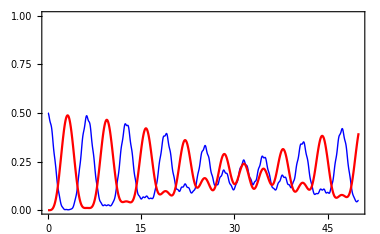

```mathematica
Plot[{f1[t/(η0 g0)],f2[t/(η0 g0)]},{t,0,50},PlotRange->{0,1},Frame->True,PlotStyle->{{Blue,Thick},Red}]
```

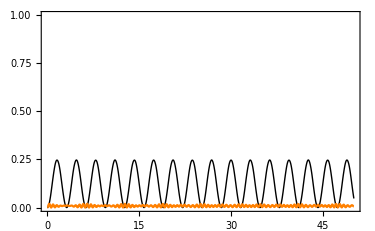

```mathematica
Plot[{f3[t/(η0 g0)],f4[t/(η0 g0)]},{t,0,50},PlotRange->{0,1},Frame->True,PlotStyle->{{Thick,Black},Orange}]
```

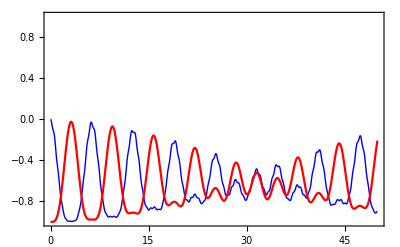

```mathematica
Plot[{inv1[t/(η0 g0)],inv2[t/(η0 g0)]},{t,0,50},PlotRange->{-1,1},Frame->True,PlotStyle->{{Blue,Thick},Red}]
```

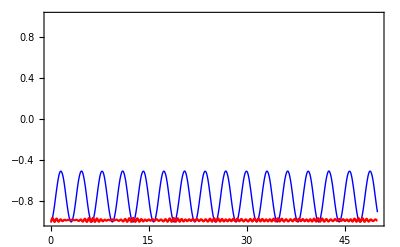

```mathematica
Plot[{inv3[t/(η0 g0)],inv4[t/(η0 g0)]},{t,0,50},PlotRange->{-1,1},Frame->True,PlotStyle->{{Blue,Thick},Red}]
```

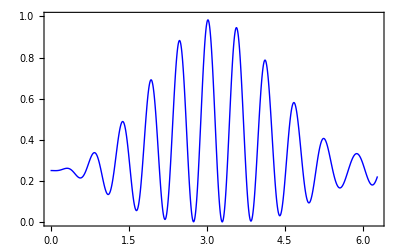

```mathematica
Plot[fid[t/(η0 g0)],{t,0,2π},PlotRange->{0,1},Frame->True,PlotStyle->{Blue,Thick}]
```

```mathematica
dt=0.00001;
tn=Range[2.,4,dt];
fn=Chop[fid[tn/(η0 g0)]];
Max[fn] (* Max fidelity *)
```

$Aborted[]

```mathematica
k=Ordering[fn,-1][[1]];
tk = k*dt + 2 (* QST time *)
```

3.02531

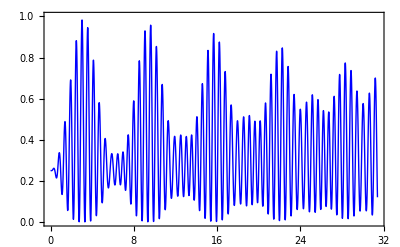

```mathematica
Plot[fid[t/(η0 g0)],{t,0,10π},PlotRange->{0,1},Frame->True,PlotStyle->{Blue,Thick}]
```

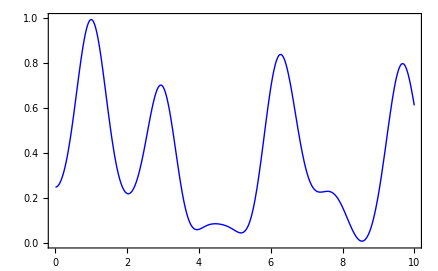

```mathematica
Plot[fid2[g],{g,0,Δ0},PlotRange->{0,1},Frame->True,PlotStyle->{Blue,Thick}]
```

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,3.5},{Δ,0.001,10},Mesh->Automatic,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

-Graphics-

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,2π},{Δ,0.001,20},Mesh->Automatic,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->65,AspectRatio->1/2,FrameLabel->{"Time (Units of ηg)","Δ (Units of ηg)"},LabelStyle->Directive[14,Black]]
```

-Graphics-

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,2π},{Δ,0.001,20},Mesh->3,MeshFunctions->{#3 &},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70,AspectRatio->1/2,FrameLabel->{"Time (Units of ηg)","Δ (Units of ηg)"},LabelStyle->Directive[14,Black]]
```

-Graphics-

```mathematica
DensityPlot[fid3D[t/(η0 g0),Δ],{t,0,2π},{Δ,0.001,20},Mesh->None,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70,AspectRatio->1/2,FrameLabel->{"Time (Units of ηg)","Δ (Units of ηg)"},LabelStyle->Directive[15,Black]]
```

-Graphics-

```mathematica
ContourPlot[fid3D2[t/(η0 g0),θ],{t,0,3.5},{θ,0,π/2},Mesh->None,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

-Graphics-

```mathematica
DensityPlot[fid3D2[t/(η0 g0),θ],{t,0,3.5},{θ,0,π/2},Mesh->None,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

-Graphics-

```mathematica
DensityPlot[fid3D2[t/(η0 g0),θ],{t,0,3.5},{θ,0,2π},Mesh->None,MeshFunctions->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->70]
```

-Graphics-

```mathematica
CF={Cos[θ],0,0,0,Sin[θ],0};
```

```mathematica
MatrixForm@CF
```

(Cos[θ]
0
0
0
Sin[θ]
0)

```mathematica
Transpose[{CF}].{CF} //MatrixForm
```

(Cos[θ]^2 | 0 | 0 | 0 | Cos[θ] Sin[θ] | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
Cos[θ] Sin[θ] | 0 | 0 | 0 | Sin[θ]^2 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Transpose[CF]
```

```mathematica
c[{Cos[θ],0,0,0,Sin[θ],0}]
```